Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 4 Coaxial cylinders
Find and sketch the potential between two coaxial cylinders of radii r_1 and r_2 having potential U_1 and U_2 , respectively.

1.  r_1=2.5 mm, r_2=2 cm, U_1=0 V, U_2=220 V

In the text example 2 on p. 759 the cylinders are considered to be infinitely long.

```mathematica
Clear["Global`*"]
```

```mathematica
Graphics3D[{Opacity[1.0],Cylinder[{{0,0,0},{0,0,15}},2.5],{Opacity[0.5],Cylinder[{{0,0,0},{0,0,15}},20]}},Boxed->False,ImageSize->200]
```

-Graphics3D-

From example 2 on text p. 759 I know that Φ = a Log[r]+b, where a and b are to be determined from boundary conditions. The text uses r as the z-variable.

```mathematica
Solve[a Log[5/2]+b==0&&a Log[20]+b==220,{a,b}]
```

{{a→-220/(Log[5/2]-Log[20]),b→(220 Log[5/2])/(Log[5/2]-Log[20])}}

I changed r_1 to fractional form to keep from getting decimals, and now I can get a better looking form because of it.

```mathematica
Simplify[-220/(Log[5/2]-Log[20])]
```

220/Log[8]

That is for a, and now, for b

```mathematica
Simplify[(220 Log[5/2])/(Log[5/2]-Log[20])]
```

-(220 Log[5/2])/Log[8]

So with this I have what I need and it only remains to put it together.

```mathematica
Φ ==220/Log[8] Log[r]-(220 Log[5/2])/Log[8]
```

Φ==-(220 Log[5/2])/Log[8]+(220 Log[r])/Log[8]

```mathematica
Simplify[-(220 Log[5/2])/Log[8]+(220 Log[r])/Log[8]]
```

(220 Log[(2 r)/5])/Log[8]

Oops, a problem.

```mathematica
PossibleZeroQ[(220 Log[(2 r)/5])/Log[8]-Re[110(1+Log[r]/Log[4])]]
```

False

Running N[•] with various values of r show that the yellow answer is indeed very different from that of the text. However, I don’t see an alternate way to do the problem. And by following what seems the exact same procedure in the next problem, the text answer is produced.

3.  r_1=10 cm, r_2=1 m, U_1=10 kV, U_2=-10 kV

```mathematica
Clear["Global`*"]
```

```mathematica
Graphics3D[{Opacity[1.0],Cylinder[{{0,0,0},{0,0,40}},10],{Opacity[0.5],Cylinder[{{0,0,0},{0,0,40}},100]}},Boxed->False,ImageSize->200]
```

-Graphics3D-

From example 2 on text p. 759 I know that Φ(r) = a Log[r]+b, where a and b are to be determined from boundary conditions. The text uses r as the z-variable.

```mathematica
Solve[a Log[10]+b==10&&a Log[100]+b==-10,{a,b}]
```

{{a→20/(Log[10]-Log[100]),b→-(10 (Log[10]+Log[100]))/(Log[10]-Log[100])}}

I can simplify the expression for a.

```mathematica
Simplify[20/(Log[10]-Log[100])]
```

-20/Log[10]

I can find the exact value of b.

```mathematica
N[-(10 (Log[10]+Log[100]))/(Log[10]-Log[100])]
```

30.

So with this I have what I need and it only remains to put it together.

```mathematica
Φ[r] ==-20/Log[10] Log[r]+30
```

Φ[r]==30-(20 Log[r])/Log[10]

The above cell matches the text answer.

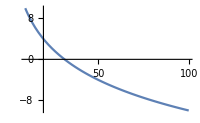

```mathematica
Plot[30-(20 Log[r])/Log[10],{r,10,100},ImageSize->200]
```

```mathematica
xtab=Flatten[Table[N[Solve[30-(20 Log[x])/Log[10]==i]],{i,-10,10}]]
```

{x→100.,x→89.1251,x→79.4328,x→70.7946,x→63.0957,x→56.2341,x→50.1187,x→44.6684,x→39.8107,x→35.4813,x→31.6228,x→28.1838,x→25.1189,x→22.3872,x→19.9526,x→17.7828,x→15.8489,x→14.1254,x→12.5893,x→11.2202,x→10.}

To find the location of the neutral cylinder,

```mathematica
N[Solve[30-(20 Log[x])/Log[10]==0]]
```

{{x→31.6228}}

I was inclined to think that the iso-lines of charge should hug the surface, but according to the developed answer equation that is not the case. They tend to hug the blue side but not the red. (Someday I hope to re-do the following super bloated graphic figure.)

```mathematica
Graphics[{{Opacity[0.9],RGBColor[0,0,1],Annulus[{0,0},{10,11.22},{0,π/2}]},{Opacity[0.8],RGBColor[0,0,1],Annulus[{0,0},{11.22,12.59},{0,π/2}]},{Opacity[0.7],RGBColor[0,0,1],Annulus[{0,0},{12.59,14.12},{0,π/2}]},{Opacity[0.6],RGBColor[0,0,1],Annulus[{0,0},{14.12,15.85},{0,π/2}]},{Opacity[0.5],RGBColor[0,0,1],Annulus[{0,0},{15.85,17.78},{0,π/2}]},{Opacity[0.4],RGBColor[0,0,1],Annulus[{0,0},{17.78,19.95},{0,π/2}]},{Opacity[0.3],RGBColor[0,0,1],Annulus[{0,0},{19.95,22.39},{0,π/2}]},{Opacity[0.2],RGBColor[0,0,1],Annulus[{0,0},{22.39,25.12},{0,π/2}]},{Opacity[0.1],RGBColor[0,0,1],Annulus[{0,0},{25.12,28.18},{0,π/2}]},{Opacity[0.05],RGBColor[0,0,1],Annulus[{0,0},{28.18,31.62},{0,π/2}]},{Opacity[0.05],RGBColor[1,0,0],Annulus[{0,0},{31.62,35.48},{0,π/2}]},{Opacity[0.1],RGBColor[1,0,0],Annulus[{0,0},{35.48,39.81},{0,π/2}]},{Opacity[0.2],RGBColor[1,0,0],Annulus[{0,0},{39.81,44.67},{0,π/2}]},{Opacity[0.3],RGBColor[1,0,0],Annulus[{0,0},{44.67,50.12},{0,π/2}]},{Opacity[0.4],RGBColor[1,0,0],Annulus[{0,0},{50.12,56.23},{0,π/2}]},{Opacity[0.5],RGBColor[1,0,0],Annulus[{0,0},{56.23,63.09},{0,π/2}]},{Opacity[0.6],RGBColor[1,0,0],Annulus[{0,0},{63.09,70.79},{0,π/2}]},{Opacity[0.7],RGBColor[1,0,0],Annulus[{0,0},{70.79,79.43},{0,π/2}]},{Opacity[0.8],RGBColor[1,0,0],Annulus[{0,0},{79.43,89.12},{0,π/2}]},{Opacity[0.9],RGBColor[1,0,0],Annulus[{0,0},{89.12,100},{0,π/2}]},{Dashed,RGBColor[.5,.5,.5], Circle[{0,0},31.62,{0,π/2}]},{Text["neutral cylinder",{40,20}]}},ImageSize->200]
```

-Graphics-

5 - 7 Parallel plates
Find and sketch the potential between the parallel plates having potentials U_1 and U_2. Find the complex potential.

5.  Plates at x_1=-5 cm, x_2=5 cm, potentials U_1=250 V, U_2=500 V respectively

This class of problem is discussed in example 1 on p. 759. In that example the coordinates used are not distinctive enough to result in a process. So I will feel around in the dark. What I do know is

```mathematica
Φ=a x + b
```

and that if the plates are at x =-1 and x=1 then the potential formula goes like

```mathematica
Φ[x]=1/2(Subscript[Φ, 1]-Subscript[Φ, 2])x+1/2(Subscript[Φ, 1]+Subscript[Φ, 2])
```

In this particular problem the plates are again separated across the y-axis. I tried several things to deduce how to apply boundary conditions, without success. I didn’t realize the procedure that worked was the same as used before in problem 3, until I ran across an example at http://physics.usask.ca/~xiaoc/phys463/notes/note1.pdf, section 1.1.2. This source told me how to apply the a x + b formula to get

```mathematica
Solve[a(-5)+b==250&&a(5)+b==500,{a,b}]
```

{{a→25,b→375}}

The above cell matches the text answer.

7.  Plates at x_1=12 cm, x_2=24 cm, potentials U_1=20 kV, U_2=8 kV respectively

```mathematica
Clear["Global`*"]
```

Applying the same procedure as in the last problem,

```mathematica
Solve[a(12)+b==20&&a(24)+b==8,{a,b}]
```

{{a→-1,b→32}}

The above cell matches the text answer.

13.  Arccos. Show that F[z_] = ArcCos[z] (defined in Problem set 13.7) gives the potential of a slit in the figure below.

```mathematica
Clear["Global`*"]
```

It appears, below, that the built-in ArcCos function spreads out a lot under the ComplexExpand command. Not that I intended to use it anyway.

```mathematica
ComplexExpand[ArcCos[z]]
```

π/2-Arg[ⅈ z+√(1-z^2)]+ⅈ Log[√(√((1-z^2)^2) Cos[1/2 Arg[1-z^2]]^2+(z+((1-z^2)^2)^(1/4) Sin[1/2 Arg[1-z^2]])^2)]

Instead, and repeating the expression presented in section 13.7,

```mathematica
arcCos[z_]=-ⅈ Log[z+√(z^2-1)]
```

-ⅈ Log[z+√(-1+z^2)]

```mathematica
turq=RGBColor[.392,.823,.98];
```

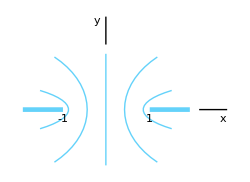

```mathematica
Graphics[{{turq,Rectangle[{14.7,5.75},{19,6.25}]},{turq,Rectangle[{1.1,5.75},{5.4,6.25}]},{turq,Line[{{10,0},{10,12}}]},{turq,Circle[{-4,6},{12,8},{-π/4,π/4}]},{turq,Circle[{-10,6},{16,3.5},{-π/5,π/5}]},{turq,Circle[{30,6},{16,3.5},{(4π)/5,(6π)/5}]},{turq,Circle[{24,6},{12,8},{(3π)/4,(5π)/4}]},{Line[{{20,6},{23,6}}]},{Line[{{10,13},{10,16}}]},{Text[Style[x,Medium],{22.5,5}]},{Text[Style[y,Medium],{9,15.5}]},{Text[Style[-1,Medium],{5.4,5}]},{Text[Style[1,Medium],{14.7,5}]}},ImageSize->250]
```

I only see the slit here. I do not presently have anything to compare it with. I do not have, and can’t seem to find, a formula or an example from which to judge the normal potential associated with a slit. I can calculate

```mathematica
arcCos[-1]
```

π

```mathematica
arcCos[1]
```

0

The text answer contains a hint, that being to use figure 391 on p. 751, which uses a sine function to map a grid onto an ellipse. The hint seems to encourage using an inverse function, of cosine, to map from the hyperbolic field lines back to a grid. Is that it? From what I learned earlier, the cosine does map vertical lines to hyperbolic, so perhaps a secant function is what I would need. But there is no guidance on how to evaluate the reverse mapping to judge if it was successful.

15.  Find the real and complex potentials in the sector -π/6≤θ≤π/6 between the boundary θ=±π/6, kept at 0 V,and the curve x^3-3x y^2=1,kept at 220 V.

```mathematica
Clear["Global`*"]
```

There is an odd artifact in the RegionPlot for this region, at the coordinate {1.5, 0.7}. Using slightly altered values (such as &&y<π/6.01 x) shows that the upper wing is not interrupted.

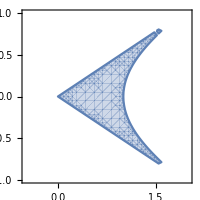

```mathematica
RegionPlot[x^3-3x y^2<1&&-π/6 x<y&&y<π/6 x,{x,-1/2,2},{y,-1,1},ImageSize->200,Axes->True
]
```

Example 3 on p. 760 deals with potentials on simple sectors. However, it would not be adequate for accomplishment of this particular problem, and I resort to the s.m., which covers it. First there is the following region to look at.

```mathematica
RegionPlot[y<x&&-y<Abs[x],{x,-1/2,2},{y,-2,2},ImageSize->100,Axes->True,AspectRatio->Automatic
]
```

-Graphics-

Consider the assertion that

```mathematica
z^2==(x+ⅈ y)^2==x^2-y^2+2 ⅈ x y
```

gives the potential in the region shown above (opening=π/2), because the real part x^2-y^2 = 0 when y = ±x. I am informed that higher powers of z give potentials in sectors of smaller openings on whose boundaries the potential is zero. And taking

```mathematica
z^3==(x+ⅈ y)^3==x^3+3 ⅈ x^2 y-3x y^2-ⅈ y^3
```

as my current case, it gives as the real potential

```mathematica
Subscript[Φ, 0]==Re[z^3]==x^3-3 x y^2==x(x^2-3 y^2)
```

and Φ will equal zero when y = ±x/(√3). The significance of this fulfillment of one boundary condition is that when x = √π it reveals the opening of the defined sector to be π/3, the very opening posed by the problem. This takes care of one boundary condition. The other one is the charged boundary at   x^3-3 x y^2, which is the real part of Φ_0. This bc does not need to be zero; in fact, it is multiplied by the charge 220, to get the answer,

220(x^3-3 x y^2)

The above cell agrees with the text answer.

In some post to MMAStackExchange, it was requested to draw a contour plot of double point field study, and it was obvious from the sample shown that it was figure 400 of the text which was the subject. So for general interest I include the best reply.

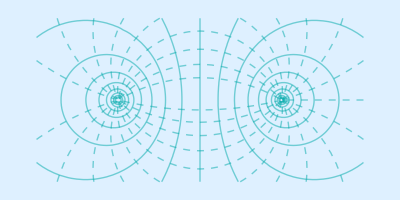

```mathematica
Options[fieldPlot]={"xMax"->1,"yMax"->1,Contours->20,"FieldLines"->20,"FieldLineStyle"->Directive[Thick,Dashed,Darker[Cyan]],"PotentialStyle"->{Directive[Thick,Darker[Cyan]]},ExclusionsStyle->None,Exclusions->None};

fieldPlot[g_,opts:OptionsPattern[]]:=Module[{im,re,xM,yM},xM=OptionValue["xMax"];
yM=OptionValue["yMax"];
im=ContourPlot[Im[g[x+I y]],{x,-xM,xM},{y,-yM,yM},ContourShading->False,ContourStyle->OptionValue["FieldLineStyle"],Contours->OptionValue["FieldLines"]];
re=ContourPlot[Re[g[x+I y]],{x,-xM,xM},{y,-yM,yM},ContourShading->False,FrameLabel->{"Re(z)","Im(z)"},ContourStyle->OptionValue["PotentialStyle"],Contours->OptionValue[Contours],Exclusions->OptionValue[Exclusions],ExclusionsStyle->OptionValue[ExclusionsStyle]];
Show[re,im,Background->LightBlue,Frame->None,AspectRatio->Automatic]]

f[z_]:=Log[z-1]-Log[z+1]

fieldPlot[f,"xMax"->2,"yMax"->1]
```